```mathematica
(*s=InputString["Enter xml file name","engine_visibility_saliency.xml"]//StringReplace[#," "->""]&;*)
s="disk_visibility_saliency.xml";
xml=Import[NotebookDirectory[]<>s];
{tfifile,volumefile,legends,{face1,face2},imagefilenames,txtfilenames,{featurefilename,visibilityfilename},path}=xml;
Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]
```

{Disk 1,Disk 2,Disk 3,Disk 4}
{left,right}
{D:\document\work\time-varying-visualization\~images\disk_saliency_chart.png,D:\document\work\time-varying-visualization\~images\disk_visibility_chart.png,D:\document\work\time-varying-visualization\~images\disk_visibility_saliency_brightness_chart.png,D:\document\work\time-varying-visualization\~images\disk_visibility_saliency_saturation_chart.png,D:\document\work\time-varying-visualization\~images\disk_visibility_saliency_weighted_chart.png}
{D:\document\work\time-varying-visualization\~images\disk_saliency_chart.txt,D:\document\work\time-varying-visualization\~images\disk_visibility_chart.txt,D:\document\work\time-varying-visualization\~images\disk_visibility_saliency_brightness_chart.txt,D:\document\work\time-varying-visualization\~images\disk_visibility_saliency_saturation_chart.txt,D:\document\work\time-varying-visualization\~images\disk_visibility_saliency_weighted_chart.txt}
{D:\document\work\time-varying-visualization\~images\disk_visibility_saliency_feature.png,D:\document\work\time-varying-visualization\~images\disk_visibility.raw}
D:\document\work\time-varying-visualization\~images\

```mathematica
d=-Graphics3D-;
cl=MorphologicalComponents[d] ;
f:=#&;
f1=Clip[(cl/.{2->0,3->0}),{0,1}]//Image3D;
f2=Clip[(cl/.{1->0,3->0}),{0,1}]//Image3D;
f3=Clip[(cl/.{1->0,2->0}),{0,1}]//Image3D;
features={f1,f2,f3}
{ImageMeasurements[f1,"TotalIntensity"]//N,ImageMeasurements[f2,"TotalIntensity"]//N,ImageMeasurements[f3,"TotalIntensity"]//N}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{4089.,6579.,4089.}

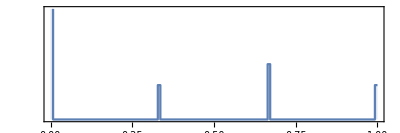

{RGBColor[{0.7725490196078432, 0.8509803921568627, 0.7333333333333333}],RGBColor[{0.8117647058823529, 0.22745098039215686, 0.8549019607843137}],RGBColor[{0.3764705882352941, 0.6313725490196078, 0.5843137254901961}]}

```mathematica
normalized=cl//Image3D//ImageAdjust;
Export[path<>"disk.raw",Flatten@ImageData[normalized,"Byte"],{"Binary","Byte"}];
ImageHistogram[normalized]
colorized=cl//Colorize;
chartcolors={PixelValue[colorized,{10,20,30}]//RGBColor,PixelValue[colorized,{20,20,20}]//RGBColor,PixelValue[colorized,{30,20,10}]//RGBColor}
```

```mathematica
disks1=Show[colorized,Boxed->False,ViewPoint->Left]
Export[path<>"disks_left.png",disks1];
disks2=Show[colorized,Boxed->False,ViewPoint->Right]
Export[path<>"disks_right.png",disks2];
```

-Graphics3D-

-Graphics3D-

```mathematica
(*(* left *)
list=Image3DSlices[d,All,3];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d3a=Image3D[list3];
d3=ImageRotate[d3a,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&*)
```

```mathematica
(*(* right *)
list=Reverse@Image3DSlices[d,All,3];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d6a=Image3D[Reverse[list3]];
d6=ImageRotate[d6a,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&*)
```

```mathematica
top:=Module[{list,count,img,list2,list3,tmp},(* top *)
list=Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
```

```mathematica
back:=Module[{list,count,img,list2,list3,tmp},(* back *)
list=Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
```

```mathematica
left:=Module[{list,count,img,list2,list3,tmp},(* left *)
list=Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
```

```mathematica
bottom:=Module[{list,count,img,list2,list3,tmp},(* bottom *)
list=Reverse@Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
```

```mathematica
front:=Module[{list,count,img,list2,list3,tmp},(* front *)
list=Reverse@Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
```

```mathematica
right:=Module[{list,count,img,list2,list3,tmp},(* right *)
list=Reverse@Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
```

```mathematica
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
{lightness,chroma,hue}=ColorSeparate[ColorConvert[colorized,"LCH"]]
opacity=ImageApply[f[#]&,d];
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
g1=ImageSubtract[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageSubtract[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
(*g3=ImageSubtract[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]]
g4=ImageSubtract[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]]*)
```

-Graphics3D-

-Graphics3D-

```mathematica
(*diff=ImageSubtract[opacity,d3]//ImageAdjust;*)
(*r=ImageApply[{1,1,1,#2}*List@@rgbafunction[#1]&,{d,diff}]//Image3D[#,ColorSpace->"RGB"]&*)
(*dog1=ImageSubtract[GaussianFilter[opacity,2],GaussianFilter[opacity,4]];
dog2=ImageSubtract[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]]
Export[path<>"disks_saliency.png",dog2];*)
```

-Graphics3D-

{0.450036,0.381473,0.16849}

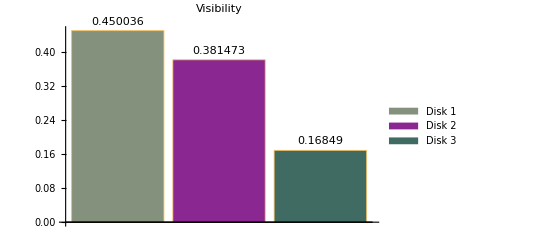

{101.865,98.2126,74.2315}

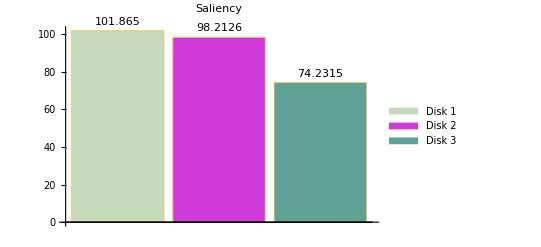

{0.534505,0.308916,0.156579}

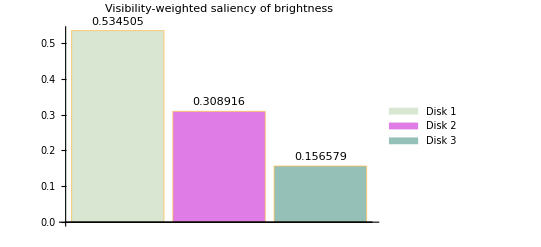

{0.15501,0.755133,0.0898567}

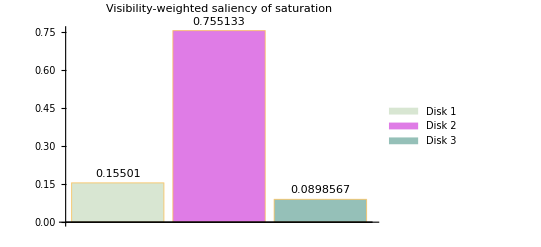

{0.344758,0.532025,0.123218}

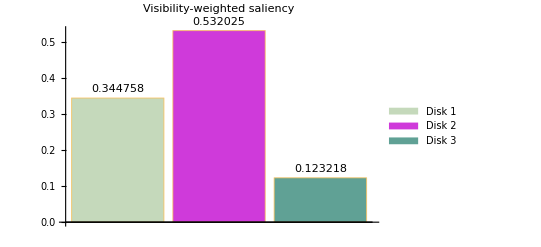

```mathematica
vis=renderslices[face1]
visibility=Table[ImageMeasurements[ImageMultiply[vis,features[[i]]],"TotalIntensity"]/ImageMeasurements[vis,"TotalIntensity"],{i,Length[features]}]
chart1=BarChart[visibility,PlotLabel->"Visibility",ChartLegends->legends,ChartStyle->(chartcolors//Darker),ChartLabels->Placed[ToString/@visibility,Above]]
dog=g1;
saliency=Table[ImageMeasurements[ImageMultiply[dog,features[[i]]],"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"],{i,Length[features]}]
chart0=BarChart[saliency,PlotLabel->"Saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@saliency,Above]]
viss=ImageMultiply[dog,vis];
vs=Table[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}]
chart2=BarChart[vs,PlotLabel->"Visibility-weighted saliency of brightness",ChartLegends->legends,ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs,Above]]
viss2=ImageMultiply[g2,vis];
vs2=Table[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}]
chart2b=BarChart[vs2,PlotLabel->"Visibility-weighted saliency of saturation",ChartLegends->legends,ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs2,Above]]
mean=Mean[{vs,vs2}]
weighted=BarChart[mean,PlotLabel->"Visibility-weighted saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@mean,Above]]
(*Export[path<>"disk_saliency_chart_left.png",chart0];
Export[path<>"disk_visibility_chart_left.png",chart1];
Export[path<>"disk_visibility_saliency_brightness_chart_left.png",chart2];
Export[path<>"disk_visibility_saliency_saturation_chart_left.png",chart2b];
Export[path<>"disk_visibility_saliency_weighted_chart_left.png",weighted];*)
charts={chart0,chart1,chart2,chart2b,weighted};
scores={saliency,visibility,vs,vs2,mean};
imagefilenames2=StringReplace[#,"."->"_left."]&/@imagefilenames;
txtfilenames2=StringReplace[#,"."->"_left."]&/@txtfilenames;
Table[Export[imagefilenames2[[i]],charts[[i]]],{i,Length[charts]}];
Table[Export[txtfilenames2[[i]],scores[[i]]],{i,Length[scores]}];
```

```mathematica
w=ImageAdd[viss,viss2]//ImageAdjust
results=ImageMultiply[w,#]&/@features
MapIndexed[Export[path<>"disks_visibility_saliency_feature"<>ToString[First[#2]]<>"_left.png",#]&,results];
```

-Graphics3D-

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

{0.16849,0.381473,0.450036}

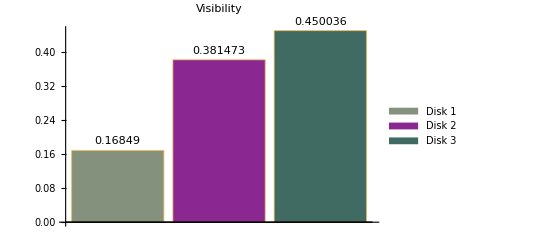

{101.865,98.2126,74.2315}

-Graphics-

{0.235268,0.338246,0.426487}

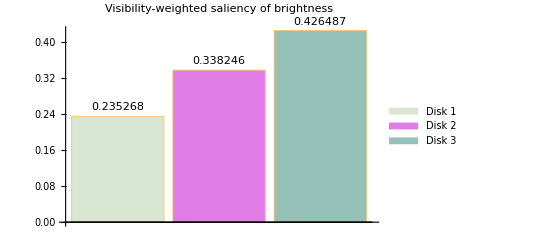

{0.0598602,0.72541,0.21473}

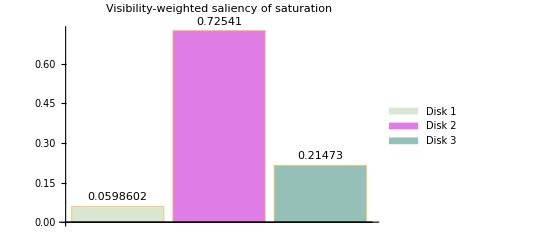

{0.147564,0.531828,0.320608}

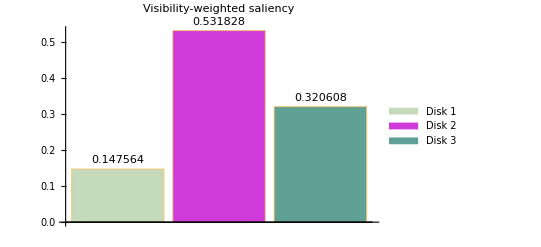

```mathematica
vis=renderslices[face2]
visibility=Table[ImageMeasurements[ImageMultiply[vis,features[[i]]],"TotalIntensity"]/ImageMeasurements[vis,"TotalIntensity"],{i,Length[features]}]
chart1=BarChart[visibility,PlotLabel->"Visibility",ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->(chartcolors//Darker),ChartLabels->Placed[ToString/@visibility,Above]]
dog=g1;
saliency=Table[ImageMeasurements[ImageMultiply[dog,features[[i]]],"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"],{i,Length[features]}]
chart0=BarChart[saliency,PlotLabel->"Saliency",ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->chartcolors,ChartLabels->Placed[ToString/@saliency,Above]]
viss=ImageMultiply[dog,vis];
vs=Table[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}]
chart2=BarChart[vs,PlotLabel->"Visibility-weighted saliency of brightness",ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs,Above]]
viss2=ImageMultiply[g2,vis];
vs2=Table[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}]
chart2b=BarChart[vs2,PlotLabel->"Visibility-weighted saliency of saturation",ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs2,Above]]
mean=Mean[{vs,vs2}]
weighted=BarChart[mean,PlotLabel->"Visibility-weighted saliency",ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->chartcolors,ChartLabels->Placed[ToString/@mean,Above]]
(*Export[path<>"disk_saliency_chart_right.png",chart0];
Export[path<>"disk_visibility_chart_right.png",chart1];
Export[path<>"disk_visibility_saliency_brightness_chart_right.png",chart2];
Export[path<>"disk_visibility_saliency_saturation_chart_right.png",chart2b];
Export[path<>"disk_visibility_saliency_weighted_chart_right.png",weighted];*)
charts={chart0,chart1,chart2,chart2b,weighted};
scores={saliency,visibility,vs,vs2,mean};
imagefilenames2=StringReplace[#,"."->"_right."]&/@imagefilenames;
txtfilenames2=StringReplace[#,"."->"_right."]&/@txtfilenames;
Table[Export[imagefilenames2[[i]],charts[[i]]],{i,Length[charts]}];
Table[Export[txtfilenames2[[i]],scores[[i]]],{i,Length[scores]}];
```

```mathematica
w=ImageAdd[viss,viss2]//ImageAdjust
results=ImageMultiply[w,#]&/@features
MapIndexed[Export[path<>"disks_visibility_saliency_feature"<>ToString[First[#2]]<>"_right.png",#]&,results];
```

-Graphics3D-

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[ImageApply[#*#2*#3&,{dog,features[[i]],d3}],{i,Length[features]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[ImageApply[#*#2*#3&,{dog,features[[i]],d6}],{i,Length[features]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Norm[List@@#]&/@ColorConvert[chartcolors,"LCH"]
```

{0.936125,1.3669,0.831608}

```mathematica
Norm[List@@#]&/@ColorConvert[chartcolors,"LAB"]
```

{0.861945,1.02841,0.661323}